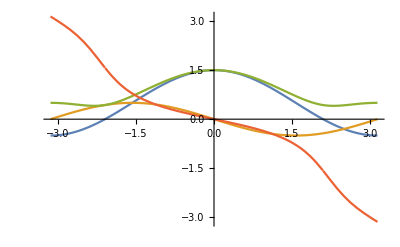

```mathematica
nn=41;
prec=5;
γ=0.5//N[#,prec]&;
J=1//N[#,prec]&;
λ=0.5//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=J(1-γ)/2//N[#,prec]&;
a2=J (1+γ)/2//N[#,prec]&;
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
Plot[{α[x],β[x],ω[x],ϕ[x]},{x,-π,π}]
```

```mathematica
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
mCos=Table[1,{k,1,(nn-1)/2}];
mCos0=1;
mSin=Table[1,{k,1,(nn-1)/2}];
mSin0=1;
MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2 ]&;
```

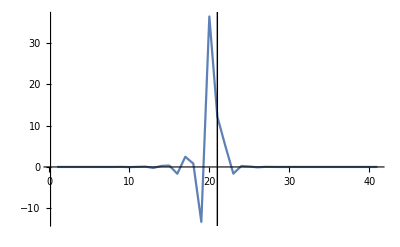

```mathematica
ListLinePlot[RotateRight[InverseFourier[MPlusBand,FourierParameters->{-1, 1}],(nn-1)/2],PlotRange->All,Epilog->{ InfiniteLine[{(nn-1)/2+1,0},{0,1}]}]
```

```mathematica
Length[MPlusBand]
```

```mathematica
ListLinePlot[RotateRight[MPlusBand,(nn-1)/2],PlotRange->{-2,6},Epilog->{ InfiniteLine[{21,0},{0,1}]}]
```

```mathematica
ListLinePlot[MPlusBand,PlotRange->{-2,6},Epilog->{ InfiniteLine[{1,0},{0,1}]}]
```